# Introducción a Mathematica

César Guerra
cesarg@wolfram.com

## Aspectos Básicos

### Sintaxis

Comandos y funciones empiezan con mayúsculas. En general los comandos tienen nombres completos del idioma inglés. Si no esta seguro de como se escribe algún comando puede escribir las primeras letras y completar la palabara usando Ctrl+k.

```mathematica
Integrate[Sin[x],x]
```

-Cos[x]

Los corchetes se usan para especificar los argumentos de un comando.

```mathematica
Factor[1-x^5]
```

-(-1+x) (1+x+x^2+x^3+x^4)

Los paréntesis se usan para agrupar expresiones matemáticas y se pueden anidar un número arbitrario de veces. Si no se usan parentesis, Mathematica usa la misma jerarquia que la usada en matemáticas.

```mathematica
(5/3+2 3-(1+2/3*5))/2
```

5/3

Las llaves se usan para agrupar un conjunto de elementos en una lista.

```mathematica
{2,🐺,Sin[x],2/3,"a"}
```

{2,🐺,Sin[x],2/3,a}

## Aspectos Básicos

### Variables

```mathematica
{x,$xx,x$,x123,xαβ,𝕩,ξ}
```

{x,$xx,x$,x123,xαβ,𝕩,ξ}

```mathematica
Sin[Log[2/(3-I)]]
```

Sin[Log[3/5+ⅈ/5]]

```mathematica
Sqrt[2.]
```

1.41421

```mathematica
calc=N[Sin[Log[2/(3-I)]]]
```

-0.465377+0.293575 ⅈ

```mathematica
calc/(√(π^3))
```

-0.0835757+0.0527222 ⅈ

Se pueden incluir comentarios usando la sintaxis: (* comentario *).

```mathematica
(* Mi calculo *)
c=Sin[Log[2/(3-I)]];(* Log en base E *)
N[c^2-c]
```

0.595767-0.56682 ⅈ

## Aspectos Básicos

### Notación técnica

Los notebooks de Mathematica permiten ingresar símbolos técnicos, expresiones matemáticas, tipos de letras, matrices, operadores, íconos, etc, usando paletas o conjugaciones de teclas.

```mathematica
({{2, 🐺}, {2, 5}})
```

{{2,🐺},{2,5}}

```mathematica
√(2/3)(α Π)/β
```

(√(2/3) α Π)/β

```mathematica
∫_3^2 Sin[x]ⅆx
```

-Cos[2]+Cos[3]

## Aspectos Básicos

### Ayuda

```mathematica
Integrate
```

```mathematica
?Integrate
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f. 
Integrate[f,{x,y,…}∈reg] integrates over the geometric region reg.

```mathematica
Integrate[Sin[Sin[x]],x]
```

∫Sin[Sin[x]]ⅆx

```mathematica
Times[a,b]
```

a b

```mathematica
Sort[{3,6,3,1,8,9}]
```

{1,3,3,6,8,9}

```mathematica
Cross
```

```mathematica
LinearSolve
```

```mathematica
?*Image*
```

ImageDimensions[image] gives the pixel dimensions of an Image or Image3D object image.

## Tipos de datos

### Expresiones Atómicas

"Atom" | "Example"
"Symbol" | "Integrate"
"Integer" | "28"
"Real" | "4.5771"
"Rational" | "2/9"
"Complex" | 3+5 ⅈ
"String" | "The rain in Spain"
"Graph" | -Graphics-
"SparseArray" | (1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 1 | 1 | 0
0 | 0 | 0 | 1)

## Tipos de datos

### Enteros y racionales

```mathematica
(7+2)4-4*5
```

16

```mathematica
6/7+12/5
```

114/35

```mathematica
25^(1/2)
```

5

### Enteros y racionales con precisión extendida

```mathematica
(9172 2916)/(5844 1413)-(2857 9248)/(6174 8779)+(1177 1161)/(3984 8155)-(4151 5946)/(6982 8319)
```

73505399860627799093943317/31033732398009095133051120

```mathematica
(91^72 29^16)/(58^44 14^13)-(28^57 92^48)/(61^74 87^79)+(11^77 11^61)/(39^84 81^55)-(41^51 59^46)/(69^82 83^19)
```

3174539591042701542412219584556347774000097024684773362794199928338497859784646755116561543400621264063846134917252325396788466522842824867832405837422750938502050672183172721393407603551319925686571948614529058427180978598246276955407583874339698435285039883731856824540003347387132673295110938865885196582719679672130786371188910757417938071891656236414384441707054636296389704902098380560185853970302522284974986026034332730986570787055415850287417464421096482074782012478847192475667205012827855652974154441634751493701724907268344914498006351333901714449311561178816727425115756847315885588685296295158702918620253182803830051215149282601158167029310380891911009409964049048534688673362049823905227665533184507495745689/3490026421268397974387548267022981777506634654865100442558988977065800978182945791294150770622373094208145134516106857379149249589320085087851815158056312225700642099419118122173490895553053229428950974381571432939489761314169850524311684590493117210218815968460315360866173961786535156386049750898629995730416887416056167265168496410110701230744053904380067875045180460353475506920926385607758384574041670098017111417351818809167906607231966791197640576107629038503608554655852501422925854501682630569779189670597431818307664867615051597851579211406792819615340830434622119740109379870174146739624308359634516895690128939807959592510799138792778235904

```mathematica
pi=N[π,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
InputForm[pi]
```

3.141592653589793

```mathematica
pi+pi^2
```

13.0111970546791518572971343831556540195108688066158964473882939685278612287054142416298082290606693

## Tipos de datos

### Reales con precisión de máquina

```mathematica
6./7+12/5
```

3.25714

```mathematica
N[6/7+12/5]
```

3.25714

```mathematica
N[6/7+12/5,16]
```

3.257142857142857

```mathematica
N[5^(1/2),20]
```

2.2360679774997896964

```mathematica
$MinMachineNumber
```

2.22507×10^-308

```mathematica
$MaxMachineNumber
```

1.79769×10^308

### Reales con precisión arbitraria

```mathematica
N[5^(1/2),40]
```

2.236067977499789696409173668731276235441

```mathematica
N[5^0.5,40]
```

2.23607

```mathematica
N[Pi,1000]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420199

```mathematica
N[Exp[Pi Sqrt[163]]]
```

2.62537×10^17

```mathematica
N[Exp[Pi Sqrt[163]],50]
```

2.6253741264076874399999999999925007259719818568888×10^17

```mathematica
$MinNumber
```

6.22968824967532196119819746965503015872`15.954589770191005*^-1355718576299610

```mathematica
$MaxNumber
```

1.60521676193366172702774105306375828321`15.954589770191005*^1355718576299609

## Tipos de datos

### Números Complejos

```mathematica
Sqrt[-17]
```

ⅈ √17

```mathematica
(1-3 I)/(2 I-3)
```

-9/13+(7 ⅈ)/13

```mathematica
N[(1-3 I)/(2 I-3)]
```

-0.692308+0.538462 ⅈ

```mathematica
N[(1-3 I)/(2 I-3),20]
```

-0.69230769230769230769+0.5384615384615384615 ⅈ

```mathematica
expI=Exp[1-7 ⅈ]
```

ⅇ^(1-7 ⅈ)

```mathematica
N[expI]
```

2.04932-1.78587 ⅈ

```mathematica
Re[expI]
```

ⅇ Cos[7]

```mathematica
Im[expI]
```

-ⅇ Sin[7]

```mathematica
Conjugate[expI]
```

ⅇ^(1+7 ⅈ)

```mathematica
Abs[expI]
```

ⅇ

## Tipos de datos

### Cadenas y Caracteres

```mathematica
string="strings and superstrings"
```

```mathematica
StringLength[string]
```

```mathematica
StringReverse[string]
```

```mathematica
StringTake[string,6]
```

```mathematica
StringDrop[string,12]
```

```mathematica
StringPosition[string,"st"]
```

```mathematica
StringInsert[string," theory",25]
```

```mathematica
StringReplace[string,"s"->"S"]
```

```mathematica
Characters[string]
```

```mathematica
ToCharacterCode[string]
```

```mathematica
FromCharacterCode[ToCharacterCode[string]-32]
```

```mathematica
ToUpperCase[string]
```

## Tipos de datos

### Símbolos (variables)

```mathematica
5^(1/10)Sin[π/6]
```

```mathematica
x^10-1//Factor
```

```mathematica
1/(4 (-1+x))-1/(4 (1+x))-1/(2 (1+x^2))//Simplify
```

```mathematica
Cos[x]^4-Sin[x]^4//Simplify
```

```mathematica
Tuples[{x,y,z},{2}]
```

## Listas y Arreglos

### Colección de Elementos

```mathematica
{a,b,c,d,e}
```

```mathematica
{{a,b},{{c}},d,{e,{f}}}
```

```mathematica
{1/(1+x/(1+x)),"first think, then code",2/3,🐺,Sin[ϵ],-Graphics3D-}
```

### Conjuntos

```mathematica
{{},{}}
```

```mathematica
{a,b,c}∪{c,d,e}
```

### Matrices

```mathematica
{{2,3},{1,2}}//MatrixForm
```

```mathematica
{{2,3},{1,2}}//Inverse
```

```mathematica
%//MatrixForm
```

### Data

```mathematica
PolyhedronData[]
```

```mathematica
PolyhedronData["Dodecahedron","VertexCoordinates"]//N
```

```mathematica
RandomReal[NormalDistribution[],{2000,2}]
```

```mathematica
Graphics[Point[%]]
```

## Listas y Arreglos

### Construcción de Listas

#### Range

```mathematica
Range[-4,14,3]
```

```mathematica
Range[4,14]
```

```mathematica
Range[14]
```

```mathematica
Range[1.5,6.3,.75]
```

#### Table

```mathematica
Table[3 k,{k,1,20,2}]
```

```mathematica
Table[i,{i,1.5,6.3,.75}]
```

```mathematica
Table[f[i],{i,10,-5,-2}]
```

```mathematica
Table[3 i,{i,2,5}]
```

```mathematica
Table[i^2,{i,4}]
```

```mathematica
Table["darwin",{8}]
```

```mathematica
Table[Random[],{8}]
```

```mathematica
Table[f[x], {x, {7,2,4,3,1,5,8,9,6,10}}]
```

```mathematica
Table[Sin[n/5],{n,0,10}]
```

```mathematica
%//N
```

```mathematica
Table[g[i,j],{j,1,4},{i,1,3}]
```

```mathematica
Table[g[i,j],{i,1,4},{j,1,3}]
```

#### Displays

```mathematica
TableForm[Table[i+j,{i,1,4},{j,1,3}]]
```

```mathematica
MatrixForm[Table[i+j,{i,1,4},{j,1,3}]]
```

```mathematica
Grid[Table[i+j,{i,1,4},{j,1,3}],Frame->All]
```

```mathematica
Table[i+j,{i,1,3},{j,1,i}]
```

```mathematica
TableForm[Table[i+j,{i,1,3},{j,1,i}]]
```

```mathematica
Table[g[i,j,k],{i,3},{j,3},{k,3}]
```

```mathematica
%//MatrixForm
```

## Listas y Arreglos

### Dimensiones y Estructura

#### TreeForm

```mathematica
TreeForm[{{{1,2},{3,4},{5,6}},{{a,b},{c,d},{e,f}}}]
```

#### Length

```mathematica
Length[{a,b,c,d,e,f}]
```

```mathematica
Length[{{{1,2},{3,4},{5,6}},{{a,b},{c,d},{e,f}}}]
```

#### Dimensions

```mathematica
Dimensions[{{{1,2},{3,4},{5,6}},{{a,b},{c,d},{e,f}}}]
```

#### ArrayDepth

```mathematica
ArrayDepth[{{{1,2},{3,4},{5,6}},{{a,b},{c,d},{e,f}}}]
```

#### Level

```mathematica
Level[{{{1,2},{3,4},{5,6}},{{a,b},{c,d},{e,f}}},{0}]
```

```mathematica
Level[{{{1,2},{3,4},{5,6}},{{a,b},{c,d},{e,f}}},{1}]
```

```mathematica
Level[{{{1,2},{3,4},{5,6}},{{a,b},{c,d},{e,f}}},{2}]
```

```mathematica
Level[{{{1,2},{3,4},{5,6}},{{a,b},{c,d},{e,f}}},{3}]
```

```mathematica
Level[{{{1,2},{3,4},{5,6}},{{a,b},{c,d},{e,f}}},3]
```

## Listas y Arreglos

### Extracción de Elementos

#### Part → [[]]

```mathematica
list={2,3,7,8,1,4}
```

```mathematica
Part[list,3]
```

```mathematica
list[[3]]
```

```mathematica
list⟦3⟧
```

```mathematica
list⟦{2,4,3}⟧
```

```mathematica
list2D={{1,2},{a,b},{3,4},{c,d},{5,6},{e,f}}
```

```mathematica
list2D[[4,1]]
```

```mathematica
list2D[[All,2]]
```

```mathematica
list2D[[{1,3,4},2]]
```

```mathematica
list2D
```

```mathematica
list2D[[3,All]]
```

```mathematica
list2D[[3,All]]
```

```mathematica
list2D⟦{2,2,1}⟧
```

```mathematica
list2D
```

```mathematica
list2D[[{1,3,4},{2,1}]]
```

```mathematica
list2D[[{1,6},2]]
```

```mathematica
list
```

#### Part [[]] y Span ;;

```mathematica
list[[2;;5]]
```

```mathematica
list2D[[2;;4,1;;1]]
```

```mathematica
tabla=Table[g[i,j],{i,1,5},{j,1,5}];
MatrixForm[tabla]
```

```mathematica
tabla[[{1,5},{1,5}]]//MatrixForm
```

```mathematica
tabla[[{2,4,4,3},{2,4,3}]]//MatrixForm
```

```mathematica
tabla[[2;;4,2;;4]]//MatrixForm
```

#### Extract

```mathematica
list2D
```

```mathematica
Extract[list2D,4]
```

```mathematica
Extract[list2D,{4}]
```

```mathematica
Extract[list2D,{{4},{5}}]
```

```mathematica
Extract[list2D,{{4,1},{5,2}}]
```

```mathematica
Part[list2D,{{4,1},{5,2}}]
```

#### Take

```mathematica
Take[{2,3,7,8,1,4},2]
```

```mathematica
Take[{2,3,7,8,1,4},-2]
```

```mathematica
Take[{2,3,7,8,1,4},{2,4}]
```

```mathematica
Take[{2,3,7,8,1,4},{2,6,2}]
```

```mathematica
Take[{2,3,7,8,1,4},{-5,-3}]
```

```mathematica
Take[{2,3,7,8,1,4},{-5,4}]
```

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[2;;3;;1,2;;3;;1]]
```

```mathematica
Take[{{a,b,c},{d,e,f},{g,h,i}},{2,3},{2,3}]
```

#### Drop

```mathematica
Drop[{2,3,7,8,1,4},2]
```

```mathematica
Drop[{2,3,7,8,1,4},-2]
```

```mathematica
Drop[{2,3,7,8,1,4},{3,5}]
```

```mathematica
Drop[{{a,b,c},{d,e,f},{g,h,i}},{2,3},{2,3}]
```

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}//MatrixForm
```

```mathematica
Drop[{{a,b,c},{d,e,f},{g,h,i}},-2,-2]
```

#### First

```mathematica
{2,3,7,8,1,4}[[1]]
```

```mathematica
First[{2,3,7,8,1,4}]
```

#### Last

```mathematica
{2,3,7,8,1,4}[[-1]]
```

```mathematica
Last[{2,3,7,8,1,4}]
```

#### Rest

```mathematica
{2,3,7,8,1,4}[[2;;-1]]
```

```mathematica
Rest[{2,3,7,8,1,4}]
```

#### Most

```mathematica
{2,3,7,8,1,4}[[1;;-2]]
```

```mathematica
Most[{2,3,7,8,1,4}]
```

## Listas y Arreglos

### Busqueda de Elementos

#### Busquedas con Select

```mathematica
Positive[3]
```

```mathematica
Positive[0]
```

```mathematica
Select[{2,3,7,8,1,4},EvenQ]
```

```mathematica
Select[{-2,3,7,-8,1,4},Positive]
```

#### Busquedas con Position y Extract

```mathematica
pos=Position[{2,3,7,8,1,4},x_/;EvenQ[x]]
```

```mathematica
Extract[{2,3,7,8,1,4},pos]
```

#### Busquedas con Pick

```mathematica
Pick[{a,b,c,d,e},{1,0,1,0,0},1]
```

```mathematica
EvenQ[{2,3,7,8,1,4}]
```

```mathematica
Pick[{2,3,7,8,1,4},EvenQ[{2,3,7,8,1,4}]]
```

## Listas y Arreglos

### Agregar y Remover Elementos

#### Insert

```mathematica
Insert[{a,b,c},x,2]
```

```mathematica
Insert[{a,b,c},x,-2]
```

#### Delete

```mathematica
Delete[{a,b,c,d},3]
```

```mathematica
Delete[{2,3,7,8,1,4},{{2},{5}}]
```

#### ReplacePart

```mathematica
ReplacePart[{a,b,c,d},x,3]
```

```mathematica
ReplacePart[{a,b,c,d},3->x]
```

```mathematica
ReplacePart[{a,b,c,d},x,{{1},{4}}]
```

#### PadLeft and PadRight

```mathematica
PadLeft[{a,b,c},10]
```

```mathematica
PadRight[{a,b,c},10]
```

```mathematica
PadRight[{a,b,c},10,x]
```

```mathematica
PadLeft[{a,b},11,{x,y,z}]
```

```mathematica
PadRight[{a,b},11,{x,y,z}]
```

```mathematica
PadLeft[{a,b,c},10,{x,y},3]
```

```mathematica
PadRight[{a,b,c},10,{x,y},3]
```

#### Prepend y Append

```mathematica
Prepend[{a,b,c},x]
```

```mathematica
Append[{a,b,c},x]
```

```mathematica
lista={a,b,c}
```

```mathematica
AppendTo[lista,x]
```

```mathematica
lista
```

```mathematica
(*evítenlo de ser posible*)
list={};
Do[
If[PrimeQ[i]===True,
AppendTo[list,i]]
,
{i,1,10}
];
list
```

#### Reap and Sow

```mathematica
x=2;Sow[x];
Reap[0;x;Sow[x+1];2;Sow[3]]
```

```mathematica
Reap[{1,Sow[2],3,Sow[4],5,6,8,9,10}]
```

```mathematica
Reap[Sum[Sow[i^2]+1,{i,10}]]
```

```mathematica
Reap[
Table[
If[PrimeQ[i]===True,
Sow[i],
i],
{i,1,10}
]
]
```

```mathematica
(*úsenlo de ser posible*)
Reap[
Do[
If[PrimeQ[i]===True,
Sow[i]]
,
{i,1,10}
]
]
```

## Listas y Arreglos

### Reordenamiento de Listas

#### Sort

```mathematica
Sort[{3,1.7,π,-4,22/7}]
```

```mathematica
Greater[3,2]
```

```mathematica
2>3
```

```mathematica
(*Second argument: test function of two vars*)
Sort[{3,1.7,π,-4,22/7},Greater]
```

```mathematica
Sort[{2,e,1,f,"d",{f},"a",n^2,1+2ⅈ}]
```

```mathematica
Sort[{2,e,1,f,"d",{f},"a",n^2,1+2ⅈ},OrderedQ[{#1,#2}]&]
```

#### Reverse

```mathematica
Reverse[{2,7,6,1,4,5}]
```

```mathematica
{2,7,6,1,4,5}[[-1;;1;;-1]]
```

```mathematica
Take[{2,7,6,1,4,5},{-1,1,-1}]
```

#### RotateLeft and RotateRight

```mathematica
RotateLeft[{1,2,3,4,5}]
```

```mathematica
RotateRight[{1,2,3,4,5},2]
```

#### Partition

```mathematica
Partition[{2,3,7,8,1,4},2]
```

```mathematica
Partition[{2,3,7,8,1,4},1,2]
```

```mathematica
Partition[{2,3,7,8,1,4},2,2]
```

```mathematica
Partition[{2,3,7,8,1,4},2,1]
```

```mathematica
Partition[{2,3,7,8,1},2,2,1]
```

```mathematica
Partition[{2,3,7,8,1},2,2,1,{}]
```

```mathematica
Partition[{2,3,7,8,1},2,2,2]
```

```mathematica
Partition[{2,3,7,8,1},2,2,2,{}]
```

```mathematica
Partition[{2,3,7,8,1},2,2,3,{w}]
```

```mathematica
Partition[{"s",2,"d",3,"r",5},2]
```

```mathematica
plots=Table[Plot[Sin[w x],{x,0,2π}],{w,{π/3,π/4,π/5,π/6,π/7}}]
```

```mathematica
GraphicsGrid[Partition[plots,3,3,1,{}],Frame->All]
```

#### Split y SplitBy

```mathematica
Split[{a,a,a,b,b,a,a,c}]
```

```mathematica
SameQ[a,b]
```

```mathematica
Split[{a,a,a,b,b,a,a,c},SameQ]
```

```mathematica
(*Second argument: test function of two vars*)
Split[{1,2,3,4,3,2,1,5,6,7,4,3},Less]
```

```mathematica
Split[{1,2,3,4,3,2,1,5,6,7,4,3},Greater]
```

```mathematica
(*Second argument: function of one var*)
SplitBy[{1,2,3,4,3,2,5,6,7,4,6,3},PrimeQ]
```

#### Gather and GatherBy

```mathematica
Gather[{a,a,a,b,b,a,a,c}]
```

```mathematica
Gather[{a,a,a,b,b,a,a,c},SameQ]
```

```mathematica
(*Second argument: function of one var*)
GatherBy[{a,a,a,b,b,a,a,c},Identity]
```

```mathematica
GatherBy[{1,2,3,4,5},OddQ]
```

```mathematica
Split[Sort[{a,b,c,a,a,c,a}]]
```

#### Transpose

```mathematica
{{5,2,7,3},{4,6,8,4}}//MatrixForm
```

```mathematica
Transpose[{{5,2,7,3},{4,6,8,4}}]//MatrixForm
```

```mathematica
{{5,2,7,3},{4,6,8,4},{6,5,3,1}}//MatrixForm
```

```mathematica
Transpose[{{5,2,7,3},{4,6,8,4},{6,5,3,1}}]//MatrixForm
```

```mathematica
Array[a,{2,2,2}]//MatrixForm
```

```mathematica
Transpose[Array[a,{2,2,2}],{1,1,2}]//MatrixForm
```

```mathematica
x=0.1Range[20];
y=Sin[x];
```

```mathematica
ListPlot[Transpose[{x,y}]]
```

```mathematica
data=Transpose[{x,y}]
```

```mathematica
abs=data[[All,1]]
```

```mathematica
ord=data[[All,2]]
```

#### Flatten

```mathematica
Flatten[{{{3,1},{2,4}},{{5,3},{7,4}}}]
```

```mathematica
Flatten[{{{3,1},{2,4}},{{5,3},{7,4}}},1]
```

```mathematica
Flatten[{{{3,1},{2,4}},{{5,3},{7,4}}},2]
```

```mathematica
tabla=Table[{p,q,BitXor[p,q]},{p,{0,1}},{q,{0,1}}]
```

```mathematica
TableForm[Flatten[tabla,1],
TableAlignments->Center,
TableHeadings->{None,{"p","q","xor[p,q]"}}]
```

## Listas y Arreglos

### Asignación de Elementos

```mathematica
l={0,1,2,3,4}
```

{0,1,2,3,4}

```mathematica
l[[1]]=10
```

10

```mathematica
l
```

{10,1,2,3,4}

```mathematica
l[[2;;4]]=0
```

0

```mathematica
l
```

{10,0,0,0,4}

```mathematica
l[[2;;4]]={15,5,25}
```

{15,5,25}

```mathematica
l
```

{10,15,5,25,4}

```mathematica
a={{1,2,3},{4,5,6}}
```

{{1,2,3},{4,5,6}}

```mathematica
a//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6)

```mathematica
a[[2,3]]=20
```

20

```mathematica
a
```

{{1,2,3},{4,5,20}}

```mathematica
b=a
```

{{1,2,3},{4,5,20}}

```mathematica
b[[1,2]]=30
```

30

```mathematica
a
```

{{1,2,3},{4,5,20}}

```mathematica
b
```

{{1,30,3},{4,5,20}}

```mathematica
MatrixForm[a]
```

(1 | 2 | 3
4 | 5 | 20)

```mathematica
a[[{1,2},{2,3}]]=0
```

0

```mathematica
a//MatrixForm
```

(1 | 0 | 0
4 | 0 | 0)

```mathematica
a[[{1,2},{2,3}]]={{1,3},{4,6}}
```

{{1,3},{4,6}}

```mathematica
a//MatrixForm
```

(1 | 1 | 3
4 | 4 | 6)

## Listas y Arreglos

### Operaciones con Listas

#### Operaciones aritméticas

```mathematica
{1,2,3,{4,{5}}}/2
```

{1/2,1,3/2,{2,{5/2}}}

```mathematica
{1,2,3,4,5}^2
```

{1,4,9,16,25}

```mathematica
2^{1,2,3,4,5}
```

{2,4,8,16,32}

```mathematica
Expand[(x^{1,2,3,4,5}-1)^5]
```

{-1+5 x-10 x^2+10 x^3-5 x^4+x^5,-1+5 x^2-10 x^4+10 x^6-5 x^8+x^10,-1+5 x^3-10 x^6+10 x^9-5 x^12+x^15,-1+5 x^4-10 x^8+10 x^12-5 x^16+x^20,-1+5 x^5-10 x^10+10 x^15-5 x^20+x^25}

#### Max, Min, Total & Tally

```mathematica
Max[{4,1,7,2}]
```

7

```mathematica
Min[{4,1,7,2}]
```

1

```mathematica
Max[{{4,1},{7,2}}]
```

7

```mathematica
Clear[a,b]
```

```mathematica
Total[{a,b,c,d}]
```

a+b+c+d

```mathematica
Tally[{a,a,b,a,c,b,a}]
```

{{a,4},{b,2},{c,1}}

#### Count, Cases and DeleteCases

```mathematica
Clear[a,b]
```

```mathematica
Count[{a,b,a,a,b,c,b},b]
```

3

```mathematica
Cases[{a,b,a,a,b,c,b},b]
```

{b,b,b}

```mathematica
DeleteCases[{a,b,a,a,b,c,b},b]
```

{a,a,a,c}

#### Set Operations

```mathematica
Union[{4,1,2},{5,1,2}]
```

{1,2,4,5}

```mathematica
Intersection[{4,2,1},{5,1,2}]
```

{1,2}

```mathematica
Complement[{2,8,7,4,8,3},{3,5,4}]
```

{2,7,8}

```mathematica
Join[{2,5,7,3},{d,a,e,j},{},{w,x,z}]
```

{2,5,7,3,d,a,e,j,w,x,z}

#### Riffle

```mathematica
Riffle[{a,b,c},x]
```

{a,x,b,x,c}

```mathematica
Riffle[{a,b,c},{x,y,z}]
```

{a,x,b,y,c,z}

#### Combinatorial

```mathematica
Subsets[{a,b,c}]
```

{{},{a},{b},{c},{a,b},{a,c},{b,c},{a,b,c}}

```mathematica
Subsets[{a,b,c},2]
```

{{},{a},{b},{c},{a,b},{a,c},{b,c}}

```mathematica
Subsets[{a,b,c},{2}]
```

{{a,b},{a,c},{b,c}}

```mathematica
Tuples[{a,b,c},2]
```

{{a,a},{a,b},{a,c},{b,a},{b,b},{b,c},{c,a},{c,b},{c,c}}

```mathematica
Tuples[{a,b,c},3]
```

{{a,a,a},{a,a,b},{a,a,c},{a,b,a},{a,b,b},{a,b,c},{a,c,a},{a,c,b},{a,c,c},{b,a,a},{b,a,b},{b,a,c},{b,b,a},{b,b,b},{b,b,c},{b,c,a},{b,c,b},{b,c,c},{c,a,a},{c,a,b},{c,a,c},{c,b,a},{c,b,b},{c,b,c},{c,c,a},{c,c,b},{c,c,c}}

```mathematica
Tuples[{a,b,c},{2,2}]
```

{{{a,a},{a,a}},{{a,a},{a,b}},{{a,a},{a,c}},{{a,a},{b,a}},{{a,a},{b,b}},{{a,a},{b,c}},{{a,a},{c,a}},{{a,a},{c,b}},{{a,a},{c,c}},{{a,b},{a,a}},{{a,b},{a,b}},{{a,b},{a,c}},{{a,b},{b,a}},{{a,b},{b,b}},{{a,b},{b,c}},{{a,b},{c,a}},{{a,b},{c,b}},{{a,b},{c,c}},{{a,c},{a,a}},{{a,c},{a,b}},{{a,c},{a,c}},{{a,c},{b,a}},{{a,c},{b,b}},{{a,c},{b,c}},{{a,c},{c,a}},{{a,c},{c,b}},{{a,c},{c,c}},{{b,a},{a,a}},{{b,a},{a,b}},{{b,a},{a,c}},{{b,a},{b,a}},{{b,a},{b,b}},{{b,a},{b,c}},{{b,a},{c,a}},{{b,a},{c,b}},{{b,a},{c,c}},{{b,b},{a,a}},{{b,b},{a,b}},{{b,b},{a,c}},{{b,b},{b,a}},{{b,b},{b,b}},{{b,b},{b,c}},{{b,b},{c,a}},{{b,b},{c,b}},{{b,b},{c,c}},{{b,c},{a,a}},{{b,c},{a,b}},{{b,c},{a,c}},{{b,c},{b,a}},{{b,c},{b,b}},{{b,c},{b,c}},{{b,c},{c,a}},{{b,c},{c,b}},{{b,c},{c,c}},{{c,a},{a,a}},{{c,a},{a,b}},{{c,a},{a,c}},{{c,a},{b,a}},{{c,a},{b,b}},{{c,a},{b,c}},{{c,a},{c,a}},{{c,a},{c,b}},{{c,a},{c,c}},{{c,b},{a,a}},{{c,b},{a,b}},{{c,b},{a,c}},{{c,b},{b,a}},{{c,b},{b,b}},{{c,b},{b,c}},{{c,b},{c,a}},{{c,b},{c,b}},{{c,b},{c,c}},{{c,c},{a,a}},{{c,c},{a,b}},{{c,c},{a,c}},{{c,c},{b,a}},{{c,c},{b,b}},{{c,c},{b,c}},{{c,c},{c,a}},{{c,c},{c,b}},{{c,c},{c,c}}}

```mathematica
Clear[x,y,z];
Tuples[{{a,b},{x,y,z}}]
```

{{a,x},{a,y},{a,z},{b,x},{b,y},{b,z}}

```mathematica
Tuples[{{a,b},{1,2,3,4},{x}}]
```

{{a,1,x},{a,2,x},{a,3,x},{a,4,x},{b,1,x},{b,2,x},{b,3,x},{b,4,x}}

```mathematica
Flatten[Table[{i,j},{i,0,9},{j,0,9}],1]
```

{{0,0},{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{0,7},{0,8},{0,9},{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{2,0},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{3,0},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{4,0},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{5,0},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{6,0},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{7,0},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{8,0},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{9,0},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9}}

```mathematica
Tuples[Range[0,9],2]
```

{{0,0},{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{0,7},{0,8},{0,9},{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{2,0},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{3,0},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{4,0},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{5,0},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{6,0},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{7,0},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{8,0},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{9,0},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9}}

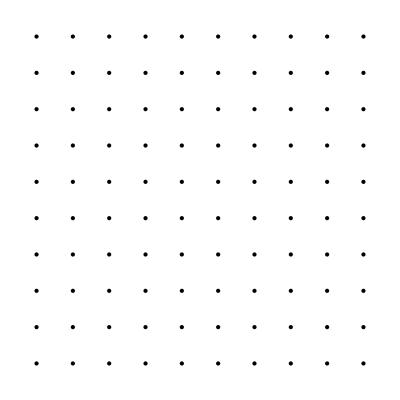

```mathematica
Graphics[Point[%]]
```

## Listas y Arreglos

### Algebra Matricial

#### Operaciones básicas

```mathematica
vector1={x1,y1}
```

```mathematica
vector2={x2,y2}
```

```mathematica
matrix1={{a1,b1},{c1,d1}}
```

```mathematica
matrix2={{a2,b2},{c2,d2}}
```

```mathematica
c vector1+vector2
```

```mathematica
c matrix1+matrix2//MatrixForm
```

```mathematica
vector1.vector2
```

```mathematica
matrix1.vector1//MatrixForm
```

```mathematica
matrix1*matrix1//MatrixForm
```

```mathematica
matrix1.matrix1//MatrixForm
```

```mathematica
vector1.matrix1
```

```mathematica
vector1.matrix1.vector2
```

#### Det, Tr y Transpose

```mathematica
Det[matrix1]
```

```mathematica
Tr[matrix1]
```

```mathematica
Transpose[matrix1]
```

#### Matrices especiales

```mathematica
IdentityMatrix[5]//MatrixForm
```

```mathematica
DiagonalMatrix[{a,b,c}]//MatrixForm
```

```mathematica
ConstantArray[0,{5,5}]//MatrixForm
```

#### Exp e Inversa

```mathematica
matrix=({{1, y}, {x, 1}});
```

```mathematica
Exp[matrix]//MatrixForm
```

```mathematica
MatrixExp[matrix]//MatrixForm
```

```mathematica
matrix^-1//MatrixForm
```

```mathematica
Inverse[matrix]//MatrixForm
```

```mathematica
Inverse[matrix].matrix//Simplify//MatrixForm
```

## Constantes y Funciones

### Constantes

#### Simbolos y valor numérico

```mathematica
{Pi,π,E,ⅇ,I,ⅈ,Degree,°,GoldenRatio}
```

{π,π,ⅇ,ⅇ,ⅈ,ⅈ,°,°,GoldenRatio}

```mathematica
{Pi,π,E,ⅇ,I,ⅈ,Degree,°,GoldenRatio}//N
```

{3.14159,3.14159,2.71828,2.71828,0.+1. ⅈ,0.+1. ⅈ,0.0174533,0.0174533,1.61803}

#### Relaciones conocidas

```mathematica
GoldenRatio==(1+Sqrt[5])/2
```

True

```mathematica
Degree==π/180
```

True

```mathematica
E^(ⅈ π)
```

-1

```mathematica
π<E
```

False

### Funciones del Sistema

#### Operan en los reales y complejos

```mathematica
Log[32]
```

Log[32]

```mathematica
Log[32.]
```

3.46574

```mathematica
N[Log[32]]
```

3.46574

```mathematica
N[Log[32],50]
```

3.4657359027997265470861606072908828403775006718013

```mathematica
Log[5.-2ⅈ]
```

1.68365-0.380506 ⅈ

#### Simplificación automática

```mathematica
Log[2,256]
```

8

```mathematica
Sin[30°]
```

1/2

```mathematica
Log[ⅈ]
```

(ⅈ π)/2

#### Operan simbólicamente

```mathematica
Log[32]
```

Log[32]

```mathematica
Log[x^n]
```

Log[x^n]

```mathematica
Refine[Log[x^n],n>0&&x>0]
```

n Log[x]

#### Operan sobre listas

```mathematica
Log[2^Range[10]]
```

{Log[2],Log[4],Log[8],Log[16],Log[32],Log[64],Log[128],Log[256],Log[512],Log[1024]}

```mathematica
Log[2,2^Range[10]]
```

{1,2,3,4,5,6,7,8,9,10}

## Constantes y Funciones

### Funciones del Usuario

f[x] = expr			A function defined for a specific value
f[x_] = expr			A function of one variable, called at definition time
f[x_] := expr      		A function of one variable, called at execution time
f[x_,y_] := expr   		A function of two variables
  
?f          			Show the definition of f
Clear[f]    			Clear all definitions for f
Remove[f]   			Remove f completely

#### Definición para valores específicos

```mathematica
Clear[f]
```

```mathematica
f[x]=Log[x^2+1]
```

Log[1+x^2]

```mathematica
f[x]
```

Log[1+x^2]

```mathematica
f[a]
```

f[a]

```mathematica
Clear[f]
```

#### Definición sin retardo

```mathematica
f[x_]=Log[x^2+1]
```

Log[1+x^2]

```mathematica
?f
```

Global`f

f[x_]=Log[1+x^2]

```mathematica
f[x]
```

Log[1+x^2]

```mathematica
f[a]
```

Log[1+a^2]


```mathematica
f[-Graphics-]
```

Log[1+-Graphics-^2]

```mathematica
x=3;
```

```mathematica
f[x_]=Log[x^2+1]
```

Log[10]

```mathematica
?f
```

Global`f

f[x_]=Log[10]

```mathematica
f[2]
```

Log[10]

```mathematica
Clear[f]
```

#### Definición con retardo

```mathematica
x=3
```

3

```mathematica
f[x_]:=Log[x^2+1]
```

```mathematica
?f
```

Global`f

f[x_]:=Log[x^2+1]

```mathematica
f[a]
```

Log[1+a^2]

```mathematica
f[12]
```

Log[145]

```mathematica
f[12.]
```

4.97673

```mathematica
f[{1,2,3}]
```

{Log[2],Log[5],Log[10]}

```mathematica
Clear[g];
g[x_,y_]:=Log[x^2 y^2+1]
```

```mathematica
g[2,a]
```

Log[1+4 a^2]

```mathematica
g[2,√3]
```

Log[13]

#### Sobrecarga de una Función

```mathematica
Clear[f]
```

```mathematica
f[π]=0;
f[x_]:=1+x+x^2
f[x_,y_]:=x+y
f[x_,y_,z_]:=1/(x+y-z)
```

```mathematica
f[2]
```

7

```mathematica
f[π]
```

0

```mathematica
f[2,1]
```

3

```mathematica
f[2,1,a]
```

1/(3-a)

```mathematica
?f
```

Global`f

f[π]=0
 
f[x_]:=1+x+x^2
 
f[x_,y_]:=x+y
 
f[x_,y_,z_]:=1/(x+y-z)

#### Ejemplo: Sinc

```mathematica
Clear[sinc]
```

```mathematica
sinc[0]=1;
sinc[x_]=Sin[x]/x
```

```mathematica
sinc[0]
```

```mathematica
Plot[sinc[x],{x,-10,10}]
```

#### Ejemplo: Alias para Random[]

```mathematica
rand1=Random[]
```

0.767178

```mathematica
rand2:=Random[]
```

```mathematica
rand1
```

0.767178

```mathematica
rand1
```

0.767178

```mathematica
rand2
```

0.404443

```mathematica
rand2
```

0.444881

```mathematica
?rand1
```

Global`rand1

rand1=0.767178

```mathematica
?rand2
```

Global`rand2

rand2:=Random[]

```mathematica
RandomInteger[{0,1},10]
```

{0,1,1,0,1,1,1,0,1,0}

```mathematica
n
```

n

```mathematica
Clear[rand]
```

```mathematica
rand[n_]:=RandomInteger[{0,1},n]
```

```mathematica
rand[10]
```

{0,0,0,1,0,0,1,1,0,1}

```mathematica
rand[100]
```

{0,0,1,0,1,1,0,1,0,0,1,1,0,1,0,1,0,1,1,0,1,0,1,1,1,1,0,0,0,0,1,1,0,0,0,1,1,1,0,1,1,0,0,1,1,1,1,1,1,1,0,0,1,1,1,1,0,1,0,1,0,0,1,0,1,0,1,0,0,1,0,1,1,1,0,1,0,1,0,0,0,0,1,0,1,0,1,0,0,0,0,1,0,0,1,0,0,1,0,0}

```mathematica
a=rand[10^6];//AbsoluteTiming
```

{0.0035957,Null}

```mathematica
b=a^2;//AbsoluteTiming
```

{0.00355165,Null}

#### Ejemplo: Valor Absoluto

```mathematica
Clear[abs]
```

```mathematica
abs[x_Complex]:=√(Re[x]^2+Im[x]^2)
abs[x_?NumberQ]:=If[x>=0,x,-x]
```

```mathematica
abs[1+ⅈ]
```

```mathematica
abs["s"]
```

```mathematica
abs[-2/3.]
```

#### Ejemplo: Caso especial de tuples

```mathematica
tuples[x_,y_]:={{x,x},{x,y},{y,x},{y,y}}
```

```mathematica
tuples[a,b]
```

```mathematica
Tuples[{a,b},2]
```

#### Ejemplos: Criba de Eratostenes

```mathematica
sieve[n_]:=Table[Prime[i],{i,PrimePi[n]}]
```

```mathematica
sieve[1000]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997}

#### Ejemplo: Filtrando data

```mathematica
fLess10Q[x_]:=x<10
```

```mathematica
fLess10Q[5]
```

True

```mathematica
Select[{2,3,54,7,1,5,7},fLess10Q]
```

{2,3,7,1,5,7}

```mathematica
Select[{2,3,54,7,1,5,7},#<10&]
```

{2,3,7,1,5,7}

## Constantes y Funciones

### Funciones Puras

Function[x, body]            		A pure function with the argument x
Function[{x,y,...}, body]    		A pure function with the arguments x, y, ...

body &    		A pure function with the argument # 
				or with the arguments #1, #2, ...; 

•  ## means all arguments supplied to a pure function;
•  ##n means all arguments from the nth to the last

#### Un argumento

```mathematica
a//Clear
```

```mathematica
Function[z,z^2][a]
```

a^2

```mathematica
squared1=Function[z,z^2]
```

Function[z,z^2]

```mathematica
squared1[w]
```

w^2

```mathematica
Function[#^2][a]
```

a^2

```mathematica
squared2=Function[#^2]
```

#1^2&

```mathematica
squared2[a]
```

a^2

```mathematica
(#^2)&[a]
```

a^2

```mathematica
squared3=(#^2)&
```

#1^2&

```mathematica
squared3[a]
```

a^2

#### Multiargumento

```mathematica
Clear[b]
```

```mathematica
Function[{x,y},x^2 y^2][a,b]
```

a^2 b^2

```mathematica
Function[#1^2#2^2][a,b]
```

a^2 b^2

```mathematica
(#1^2+#2^2)&[w,q]
```

q^2+w^2

```mathematica
(#1^2+#3^2)&[q,w,e]
```

e^2+q^2

```mathematica
Clear[f]
```

```mathematica
f[#1,#2]&[a,b,c,d]
```

f[a,b]

```mathematica
f[##]&[a,b,c,d]
```

f[a,b,c,d]

```mathematica
f[##]&[a,b,c,d,e,f]
```

f[a,b,c,d,e,f]

```mathematica
f[X,##,Y,##]&[a,b,c,d]
```

f[X,a,b,c,d,Y,a,b,c,d]

```mathematica
f[X,#1,Y,#2,z,##]&[a,b,c,d]
```

f[X,a,Y,b,z,a,b,c,d]

#### Tres formas de aplicacion

```mathematica
{f[a],f@a,a//f}
```

```mathematica
{f[a,b],f@Sequence[a,b],Sequence[a,b]//f}
```

```mathematica
{f[a,b,c,d,e,f],f[a,b,c,Sequence[d,e],f]}
```

```mathematica
Log[32]//N
```

```mathematica
Log[32]//N[#,50]&
```

```mathematica
#1^2#2^2&[a,b]
```

```mathematica
#1^2#2^2&@Sequence[a,b]
```

```mathematica
Sequence[a,b]//#1^2#2^2&
```

#### Ejemplo: Funciones que crean funciones

```mathematica
buildFunction=Function[{f},f[#1,#2]&]
```

```mathematica
buildFunction[h]
```

```mathematica
buildFunction[h][m,n]
```

```mathematica
buildFunction=Function[{f,x,y},f[x,y,#]&]
```

```mathematica
buildFunction[h,a,b]
```

```mathematica
buildFunction[f,a,b][s]
```

#### Ejemplo: Filtrando data

```mathematica
data = { 24.39001, 29.669, 9.321, 20.8856, 23.4736, 22.1488, 24.7434, 22.1619, 21.1039, 24.8177, 27.1331, 25.8705, 39.7676, 24.7762};
```

```mathematica
ListPlot[data,PlotRange->{0,30}]
```

```mathematica
20≤#≤30&[25]
```

```mathematica
Select[data,20≤#≤30&]
```

```mathematica
ListPlot[Select[data,20≤#≤30&],PlotRange->{0,30}]
```